```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
test[x_]:=Sin[Pi x]^2
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
hierarchicalCoefficients[f_,l_]:=Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct[coefficients_]:=Sum[Sum[coefficients[[l,i]] ϕ[2^l(x-2^-l(2i-1))],{i,1,Length[coefficients[[l]]]}],{l,1,Length[coefficients]}]
```

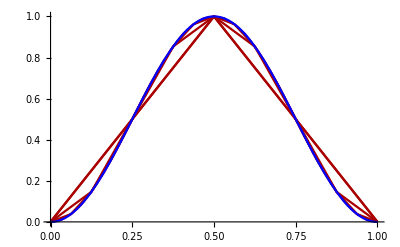

```mathematica
Show[Plot[Table[Reconstruct[N[hierarchicalCoefficients[test,n]]],{n,1,5}],{x,0,1},PlotStyle->{Darker[Red]}],Plot[test[x],{x,0,1},PlotStyle->Blue]]
```

```mathematica
Animate[Plot[{test[x],Reconstruct[N[hierarchicalCoefficients[test,n]]]},{x,0,1}],{n,1,5},AnimationRunning->False]
```

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
```

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]
hierarchicalCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]
Reconstruct2D[coefficients_]:=Sum[Sum[coefficients[[lx,ly,i,j]] ϕ[2^lx(x-2^-lx(2i-1))] ϕ[2^ly(y-2^-ly(2j-1))],{i,1,Length[coefficients[[lx,ly]]]},{j,1,Length[coefficients[[lx,ly,i]]]}],{lx,1,Length[coefficients]},{ly,1,Length[coefficients]}]
```

```mathematica
Plot3D[{test2D[x,y],Reconstruct2D[hierarchicalCoefficients2D[test2D,3,3]]},{x,0,1},{y,0,1},PlotStyle->{Opacity[.5],Opacity[1]}]
```

-Graphics3D-

```mathematica
error=Table[NIntegrate[(test[x]-Reconstruct[N[hierarchicalCoefficients[test,n]]])^2,{x,0,1}],{n,1,7}]
```

{0.00569097,0.00569097,0.000385815,0.0000246062,1.54567×10^-6,9.67266×10^-8,6.04732×10^-9}

```mathematica
error=Sqrt[error]
```

{0.0754385,0.0754385,0.0196422,0.00496046,0.00124325,0.000311009,0.0000777645}

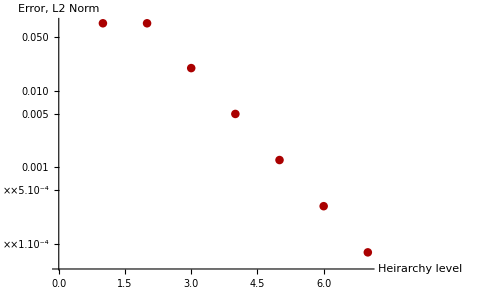

```mathematica
ListLogPlot[error,PlotStyle->{Darker[Red],Thick},AxesLabel->{"Heirarchy level","Error, L2 Norm"}]
```

```mathematica
LinearModelFit[Table[{i,Log2[error][[i]]},{i,2,Length[error]}],x,x]
```

FittedModel[0.274201-1.98711 x]

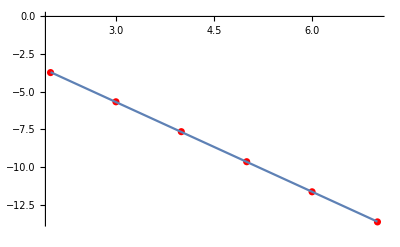

```mathematica
Show[ListPlot[Table[{i,Log2[error]⟦i⟧},{i,2,Length[error]}],PlotStyle->Red],Plot[%176[x],{x,2,7}]]
```

We go as C 2^(-1.99 l) where l is the level, which is in turn equal to the log base 2 of the number of gridpoints. So we have that the error decays as N^-2 as expected.

```mathematica
error2D=Table[NIntegrate[(test2D[x,y]-Reconstruct2D[N[hierarchicalCoefficients2D[test2D,n,n]]])^2,{x,0,1},{y,0,1}],{n,1,5}]
```

{0.00488296,0.00488296,0.000359046,0.0000234061,1.47851×10^-6}

```mathematica
error2D=Sqrt[error2D]
```

{0.0698782,0.0698782,0.0189485,0.00483798,0.00121594}

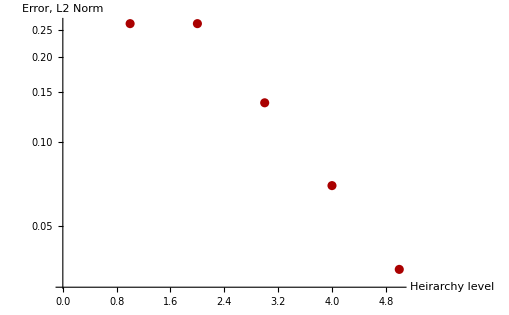

```mathematica
ListLogPlot[Sqrt[error2D],PlotStyle->{Darker[Red],Thick},AxesLabel->{"Heirarchy level","Error, L2 Norm"}]
```

```mathematica
LinearModelFit[Table[{2i,Log2[error2D][[i]]},{i,2,Length[error2D]}],x,x]
```

FittedModel[0.0923279-0.975185 x]

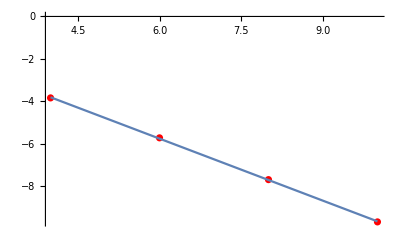

```mathematica
Show[ListPlot[Table[{2 i,Log2[error2D]⟦i⟧},{i,2,Length[error2D]}],PlotStyle->Red],Plot[%180[x],{x,4,10}]]
```

This is the log2 error vs. the 1-norm of the hierarchy level vector l. 

Note that although the slope is .98 and not 1, if we were to take successive differences in the logs of the error, we get a slope coming closer and closer to 1:

```mathematica
-(Log2[error2D][[5]]-Log2[error2D][[4]])/2
```

0.996168